# Лабораторная работа №5

## Методы решения уравнения переноса

## Вариант 3, задача 1

## Условие задачи

Дифференциальная задача

Piecewise[{{(∂u)/(∂t)-2(∂u)/(∂x)=0;, 0<t≤ 1, 0≤ x<1;}, {u[x,0]=Cos[x];, u[1,t]=Cos[1+2t];}}]

Разностная схема

D_h={(x_l,t^n):x_l=h l, h L=1, l= OverBar[0,L]; t^n=n τ; τ N=1, n= OverBar[0,N]},Piecewise[{{u_l^(n+1)= u_l^n+τ/(3h)(2 u_(l+3)^n-9 u_(l+2)^n+18 u_(l+1)^n-11 u_l^n)+(2 τ^2)/h^2(-u_(l+3)^n+4 u_(l+2)^n-5 u_(l+1)^n+2 u_l^n)+(4 τ^3)/(3 h^3)(u_(l+3)^n-3 u_(l+2)^n+3 u_(l+1)^n-u_l^n), l= OverBar[0, L-3],n= OverBar[0,N-1]}, {u_l^0=Cos[x_l], l= OverBar[0,L]}, {u_L^n=Cos[1+2 t^n], n= OverBar[1,N]}, {u_(L-1)^n=?, n= OverBar[1,N]}, {u_(L-2)^n=?, n= OverBar[1,N]}}]

## Решение

### Основные этапы:

Аналитическое решение дифференциальной задачи и построение следа в выбранном конечномерном пространстве;

Вывод дополнительных разностных уравнений, где это необходимо;

Исследование разностной схемы на аппроксимацию и спектральную устойчивость, используя принцип замороженных коэффициентов;

Разработка алгоритма решения разностной задачи и его реализация в виде программы, написанной на алгоритмическом языке высокого уровня;

Отладка программы с учетом вычисленных значений следа аналитического решения;

Проведение практических исследований свойств используемой разностной схемы на последовательно удваиваемых сетках:

соответствует ли порядок сходимости численного решения порядку аппроксимации на решении, установленному в пункте 3;

насколько сильно зависят численные результаты от выполнения условий устойчивости и что происходит, когда они нарушаются;

как изменится порядок сходимости, если при задании дополнительных разностных уравнений оставить меньшее число слагаемых в разложении в ряд Тейлора значений следа;

предложить и опытным путем проверить свои варианты задания дополнительных граничных уравнений;

выяснить, насколько сильно значения решения при t=1 зависят от начальных или граничных условий, и объяснить полученный результат.

## Аналитическое решение задачи

Найдем аналитическое решение уравнения:

```mathematica
pde=D[u[x,t],t]-2D[u[x,t],x]==0;
sol=DSolve[{pde,u[x,0]==Cos[x]},u[x,t],{x,t}]
analyticPlot=Plot3D[u[x,t]/.sol,{x,-1,1},{t,-1,1}]
```

{{u[x,t]→Cos[2 t+x]}}

-Graphics3D-

Установим решение в качестве функции для вычисления значений на сетке:

```mathematica
AnalyticEval[x_,t_]:=N[Cos[2 t+x]];
```

В качестве конечномерного пространства, на котором будет происходить сравнение получаемых на последовательно удваиваемых сетках численных решений, предлагается брать D_n={(x,t=1):x_l=h l, h L=1, l= OverBar[0,L], L=10}, т.е. равномерную по x сетку с одиннадцатью узлами, расположенными на временном слое t=T=1. Следующим шагом является построение следа, т.е. вычисление значений аналитического решения в одиннадцати равноудаленных точках при t=1.

```mathematica
L=10;
trail=Table[AnalyticEval[x,1],{x,0,1,1/L}]
```

{-0.416147,-0.504846,-0.588501,-0.666276,-0.737394,-0.801144,-0.856889,-0.904072,-0.942222,-0.970958,-0.989992}

## Построение разностных схем

Разностная схема дана в условии задачи. Однако нам не хватает разностных уравнений u_(L-1)^n, n= OverBar[1,N] и u_(L-2)^n, n= OverBar[1,N].

Запишем разложение значений следа ([u]_l)^n, n= OverBar[1,N] в ряд Тейлора до третьего порядка по h включительно:

[u]_l^n=[u]_0^n+[u_x']_0^n h+[u_(x x)'']_0^n h^2/2+[u_(x x x)''']_0^n h^3/6+O[h^4].

Для нахождения [u_x']_0^n, [u_(x x)'']_0^n можно воспользоваться формулами:

[u'_x]_0^n=1/a_0^n(-[ (u̇)_t]_0^n+b_0^n), n= OverBar[1,N]

[u''_(x x)]_0^n=1/((a_0^n)^2){((ψ^(..))_(t t))_0^n+[((ȧ)_t)_0^n-(a_0^n(a'_x))_0^n]1/a_0^n[b_0^n-((ψ̇)_t)_0^n]-((ḃ)_t)_0^n+(a_0^n(b'_x))_0^n

Третью частную производную по x будем выражать через третью частную производную по времени, последовательно выполняя следующие преобразования: во-первых, вычислим частную производную по времени от левой и правой частей уравнения

(∂^2 u)/(∂t^2)=a^2(x,t)(∂^2 u)/(∂x^2)-[(∂a(x,t))/(∂t)-a(x,t)(∂a(x,t))/(∂x)](∂u(x,t))/(∂x)+(∂b(x,t))/(∂t)-a(x,t)(∂b(x,t))/(∂x)

и получим:

(∂^3 u)/(∂t^3)=a^2(∂^3 u)/(∂t∂x^2)+2a(∂a)/(∂t)(∂^2 u)/(∂x^2)-[(∂a)/(∂t)-a(∂a)/(∂x)](∂u^2)/(∂t∂x)-[(∂^2 a)/(∂t^2)-a(∂^2 a)/(∂t∂x)-(∂a)/(∂t)(∂a)/(∂x)](∂u)/(∂x)+(∂^2 b)/(∂t^2)-a(∂^2 b)/(∂t∂x)-(∂a)/(∂t)(∂b)/(∂x)

Также определим

(∂^2 u)/(∂x∂t)=-a(x,t)(∂^2 u)/(∂x^2)-(∂a)/(∂x)(∂u)/(∂x)+(∂b)/(∂x)

и продифференцируем один раз по x:

(∂^3 u)/(∂x^2∂t)=-a(x,t)(∂^3 u)/(∂x^3)-2(∂a)/(∂x)(∂^2 u)/(∂x^2)-(∂^2 a)/(∂x^2)(∂u)/(∂x)+(∂^2 b)/(∂x^2)

Подставим эти два выражения, умноженные на a^2(x,t) в (1) и разрешим относительно третьей частной производной по x при x=0 и t=t^n:

[u'''_(x x x)]_0^n=-(1/((a_0^n)^3)[(u^(...))_(t t t)])_0^n+(3/((a_0^n)^2)[(OverDot[a_t])_0^n-(a_0^n(a'_x))_0^n][u''_(x x)])_0^n-1/((a_0^n)^3){((a^(..))_(t t))_0^n-(a_0^n((ȧ')_(t x)))_0^n+(a_0^n)^2(a''_(x x))_0^n-2( (ȧ)_t)_0^n(a'_x)_0^n+(a_0^n[(a'_x)_0^n])^2}×[u'_x]_0^n+1/((a_0^n)^3)[((b^(..))_(t t))_0^n-(a_0^n((ḃ')_(t x)))_0^n+(a_0^n)^2(b''_(x x))_0^n-2((ȧ)_t)_0^n(b'_x)_0^n+(a_0^n(a'_x))_0^n(b'_x)_0^n]

где значения [u'_x]_0^n и [u_(x x)^(' ')]_0^n найдены в пособии.

Найдем все недостающие члены разложения:

[u]_0^n:

[u'_x]_0^n=1/a_0^n(-[(u̇)_t]_0^n+b_0^n), n=OverBar[1,N], где [(u̇)_t]_0^n=((ψ̇)_t)_0^n, n=OverBar[1,N].

[u''_(x x)]_0^n:

[u''_(x x)]_0^n=1/((a_0^n)^2){((ψ̈)_(t t))_0^n+[((ȧ)_t)_0^n-(a_0^n(a'_x))_0^n]1/a_0^n[b_0^n-((ψ̇)_t)_0^n]-((ḃ)_t)_0^n+(a_0^n(b'_x))_0^n}.

В данной задаче a_l^n=a(x_l,t^n)≡2, b_l^n=b(x_l,t^n)≡0, [u]_l^n=u(x_l,t^n)=cos(2 t^n+x_l)=cos(2 n τ+h l). Для упрощения, напишем несколько вспомогательных функций:

```mathematica
ClearAll[n]
a[x_,t_]=2;
b[x_,t_]:=0;
u[x_,t_]:=Cos[2 t+x];
InNet[eq_,l_,n_]:=eq/.{t->2n*1/(Nm+1),x->l*1/(L+1)}; (*То же самое Subscript[что [eq], l]^n*)
```

```mathematica
u1x=(1/("a_0^n")(-"[(u̇)_t]_0^n"+"b_0^n"))/.{"a_0^n"-> InNet[a[x,t],0,n],"[(u̇)_t]_0^n"-> InNet[D[u[x,t],t],0,n],"b_0^n"->InNet[ b[x,t],0,n]}
```

Sin[(4 n)/(1+Nm)]

```mathematica
u2x=(1/(("a_0^n")^2)("((ψ̈)_(t t))_0^n"+("((ȧ)_t)_0^n"-"a_0^n""(a'_x)_0^n")1/("a_0^n")("b_0^n"-"((ψ̇)_t)_0^n")-"((ḃ)_t)_0^n"+"a_0^n""(b'_x)_0^n"))/.{"a_0^n"-> InNet[a[x,t],0,n],"((ψ̇)_t)_0^n"-> InNet[D[u[x,t],t],0,n],"b_0^n"-> InNet[b[x,t],0,n],"((ψ̈)_(t t))_0^n"-> InNet[D[u[x,t],{x,2}],0,n],"((ȧ)_t)_0^n"-> InNet[D[a[x,t],t],0,n],"(a'_x)_0^n"->InNet[D[a[x,t],x],0,n],"((ḃ)_t)_0^n"-> InNet[D[b[x,t],t],0,n],"(b'_x)_0^n"->InNet[D[b[x,t],x],0,n] }
```

-1/4 Cos[(4 n)/(1+Nm)]

```mathematica
u3x=-1/(("a_0^n")^3)"[(u^(...))_(t t t)]_0^n"+3/(("a_0^n")^2)("(OverDot[a_t])_0^n"-"a_0^n""(a'_x)_0^n")"[u''_(x x)]_0^n"-1/(("a_0^n")^3)("((a^(..))_(t t))_0^n"-"a_0^n""((ȧ')_(t x))_0^n"+("a_0^n")^2"(a''_(x x))_0^n"-2"((ȧ)_t)_0^n""(a'_x)_0^n"+"a_0^n"("(a'_x)_0^n")^2)*"[u'_x]_0^n"+1/(("a_0^n")^3)("((b^(..))_(t t))_0^n"-"a_0^n""((ḃ')_(t x))_0^n"+("a_0^n")^2"(b''_(x x))_0^n"-2"((ȧ)_t)_0^n""(b'_x)_0^n"+"a_0^n""(a'_x)_0^n""(b'_x)_0^n")/.{"a_0^n"-> InNet[a[x,t],0,n],"((ψ̇)_t)_0^n"-> InNet[D[u[x,t],t],0,n],"b_0^n"-> InNet[b[x,t],0,n],"((ψ̈)_(t t))_0^n"-> InNet[D[u[x,t],{x,2}],0,n],"((ȧ)_t)_0^n"-> InNet[D[a[x,t],t],0,n],"(a'_x)_0^n"->InNet[D[a[x,t],x],0,n],"((ḃ)_t)_0^n"-> InNet[D[b[x,t],t],0,n],"(b'_x)_0^n"->InNet[D[b[x,t],x],0,n] ,"[(u^(...))_(t t t)]_0^n"->InNet[D[u[x,t],{t,3}],0,n],"((b^(..))_(t t))_0^n"->InNet[D[b[x,t],{t,2}],0,n],"(b''_(x x))_0^n"-> InNet[D[b[x,t],{x,2}],0,n],"((ḃ')_(t x))_0^n"-> InNet[D[b[x,t],t,x],0,n],"((a^(..))_(t t))_0^n"-> InNet[D[a[x,t],{t,2}],0,n],"(a'_x)_0^n"-> InNet[D[a[x,t],x],0,n],"(a''_(x x))_0^n"-> InNet[D[a[x,t],{x,2}],0,n],"((ȧ')_(t x))_0^n"-> InNet[D[a[x,t],t,x],0,n],"(OverDot[a_t])_0^n"-> InNet[D[a[x,t],t],0,n]}
```

-Sin[(4 n)/(1+Nm)]

Получаем формулу для разложения:

```mathematica
ru[l_,n_]:=N[(InNet[u[x,t],0,n]+InNet[u1x,0,n]*h*2+InNet[u2x,0,n]*(l*h*2)^2/2+InNet[u3x,0,n]*(l*h*2)^3/6)/.h-> 1/L];
```

Таким образом, формула для u_(L-1)^n имеет вид:

```mathematica
Clear[n];
ru[1,n]
```

0.995 Cos[(4. n)/(1.+Nm)]+0.198667 Sin[(4. n)/(1.+Nm)]

Формула для u_(L-2)^n:

```mathematica
Clear[n];
ru[2,n]
```

0.98 Cos[(4. n)/(1.+Nm)]+0.189333 Sin[(4. n)/(1.+Nm)]

## Вычисление значений в точках

Выделяем необходимый массив точек и заполняем первый слой согласно первому граничному условию:

```mathematica
ClearAll[numerical]
h=1/L;
τ=h*0.75;
Nm=1/τ;
numerical=Table[0,{t,Nm+1},{x,L+1}];
For[l=1,l<=L+1,l++,
numerical[[1,l]]=N[Cos[1/L*l]];
]
MatrixForm[numerical]
```

(0.995004 | 0.980067 | 0.955336 | 0.921061 | 0.877583 | 0.825336 | 0.764842 | 0.696707 | 0.62161 | 0.540302 | 0.453596
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Теперь заполняем согласно второму граничному условию:

```mathematica
For[n=2,n<=Nm+1,n++,
numerical[[n,L+1]]=N[Cos[1+2*1/Nm*n]];
]
MatrixForm[numerical]
```

(0.995004 | 0.980067 | 0.955336 | 0.921061 | 0.877583 | 0.825336 | 0.764842 | 0.696707 | 0.62161 | 0.540302 | 0.453596
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.267499
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.120503
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0291995
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.178246
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.32329
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.461073
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.588501
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.702713
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.801144
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.881582
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.942222
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.981702
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.999135)

Теперь воспользуемся полученными выражениями для u_(L-1)^n и u_(L-2)^n:

```mathematica
For[n = 2, n <= Nm+1, n++,
 numerical[[n,L-1]] = N[(numerical[[n,L+1]]+InNet[u1x,0,n]*h*2+InNet[u2x,0,n]*(h*2)^2/2+InNet[u3x,0,n]*(h*2)^3/6)/.h-> 1/L];
 numerical[[n,L]] = N[(numerical[[n,L+1]]+InNet[u1x,0,n]*h+InNet[u2x,0,n]*h^2/2+InNet[u3x,0,n]*h^3/6)/.h-> 1/L];;
 ]
MatrixForm[numerical]
```

(0.995004 | 0.980067 | 0.955336 | 0.921061 | 0.877583 | 0.825336 | 0.764842 | 0.696707 | 0.62161 | 0.540302 | 0.453596
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.368473 | 0.319311 | 0.267499
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.26472 | 0.19382 | 0.120503
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.147102 | 0.0599493 | -0.0291995
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.016498 | -0.0801635 | -0.178246
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.125171 | -0.223862 | -0.32329
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.27491 | -0.367994 | -0.461073
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.428698 | -0.508973 | -0.588501
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.581635 | -0.64289 | -0.702713
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.728159 | -0.765653 | -0.801144
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.862338 | -0.873171 | -0.881582
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.978208 | -0.961541 | -0.942222
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.07013 | -1.02726 | -0.981702
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.13317 | -1.0674 | -0.999135)

Наконец, используем рекурсивную формулу для заполнения остальных точек:

```mathematica
For[n=1,n≤ Nm,n++,
For[l=1,l≤ L-2,l++,
numerical[[n+1,l]]=numerical[[n,l]]+τ/(3h)(2numerical[[n,l+3]]-9numerical[[n,l+2]]+18numerical[[n,l+1]]-11numerical[[n,l]])+(2 τ^2)/h^2(-numerical[[n,l+3]]+4numerical[[n,l+2]]-5numerical[[n,l+1]]+2numerical[[n,l]])+(4 τ^3)/(3 h^3)(numerical[[n,l+3]]-3numerical[[n,l+2]]+3numerical[[n,l+1]]-numerical[[n,l]])
]
]
MatrixForm[N[numerical]]
```

(0.995004 | 0.980067 | 0.955336 | 0.921061 | 0.877583 | 0.825336 | 0.764842 | 0.696707 | 0.62161 | 0.540302 | 0.453596
0.96891 | 0.939371 | 0.900445 | 0.852523 | 0.796082 | 0.731687 | 0.659982 | 0.581682 | 0.368473 | 0.319311 | 0.267499
0.921057 | 0.877578 | 0.825332 | 0.764839 | 0.696703 | 0.629676 | 0.473256 | 0.333805 | 0.26472 | 0.19382 | 0.120503
0.852519 | 0.796078 | 0.731179 | 0.668707 | 0.555992 | 0.398072 | 0.294978 | 0.229535 | 0.147102 | 0.0599493 | -0.0291995
0.764006 | 0.702932 | 0.618315 | 0.476431 | 0.340745 | 0.260965 | 0.189675 | 0.103945 | 0.016498 | -0.0801635 | -0.178246
0.665674 | 0.550565 | 0.404707 | 0.29683 | 0.225692 | 0.14782 | 0.060905 | -0.031168 | -0.125171 | -0.223862 | -0.32329
0.477184 | 0.346099 | 0.259386 | 0.187742 | 0.10525 | 0.0153115 | -0.0777561 | -0.174178 | -0.27491 | -0.367994 | -0.461073
0.299027 | 0.2233 | 0.147639 | 0.0609418 | -0.0308171 | -0.125488 | -0.224753 | -0.32193 | -0.428698 | -0.508973 | -0.588501
0.186155 | 0.105297 | 0.0155607 | -0.0776834 | -0.174964 | -0.272873 | -0.376371 | -0.470538 | -0.581635 | -0.64289 | -0.702713
0.0612028 | -0.0305899 | -0.126032 | -0.223529 | -0.324855 | -0.42298 | -0.528144 | -0.615467 | -0.728159 | -0.765653 | -0.801144
-0.0779544 | -0.174413 | -0.274153 | -0.373678 | -0.476237 | -0.571335 | -0.674927 | -0.751731 | -0.862338 | -0.873171 | -0.881582
-0.224091 | -0.323739 | -0.425234 | -0.523721 | -0.624274 | -0.712891 | -0.811158 | -0.874142 | -0.978208 | -0.961541 | -0.942222
-0.374559 | -0.474536 | -0.574615 | -0.668725 | -0.763626 | -0.842287 | -0.931153 | -0.977586 | -1.07013 | -1.02726 | -0.981702
-0.524942 | -0.621994 | -0.717142 | -0.803334 | -0.888734 | -0.954139 | -1.02944 | -1.05733 | -1.13317 | -1.0674 | -0.999135)

-Graphics3D-

-Graphics3D-

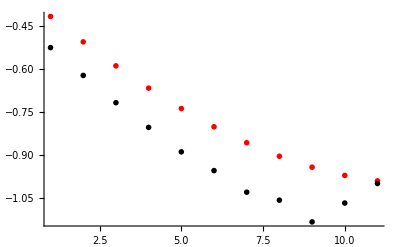

```mathematica
Plot3D[u[x,t]/.sol,{x,0,1},{t,0,1}]
ListPlot3D[numerical]
Show[ListPlot[trail,PlotStyle-> Red,PlotRange->{{0,12},{0,-1.2}}],ListPlot[numerical[[n,All]]]]
```

```mathematica
deltas=trail-numerical[[n,All]]
```

{0.108795,0.117148,0.12864,0.137058,0.151341,0.152996,0.172553,0.153254,0.190946,0.0964415,0.00914265}

```mathematica
Max[deltas]
```

0.190946